```mathematica
Clear[alpha,s,me,mmu,mme,Emu,coseMinLA,cosmMinLA,coseMinCM,EeMinLA,GevToBarn,mW,mZ,mH,WidZ,mA,xi,v];
ClearAll["Global`*"];
(*choose precision digits*)
np=100;
(*to micro-barn*)
GevToBarn=SetPrecision[0.3893793721*10^3,np];
alpha=SetPrecision[1/137.03599907430637,np];
e=SetPrecision[Sqrt[alpha*4*Pi],np];
Emu = 150;(*GeV*)
mme=SetPrecision[0.510998928*10^-3,np];(*GeV*)
mmu=SetPrecision[105.6583715*10^-3,np];(*GeV*)
coseMinLA=Cos[1/10];(*Exp cut angle*)
cosmMinLA=coseMinLA;(*Exp cut angle*)
coseMinCM = SetPrecision[0.9,np];
EeMinLA=SetPrecision[1,np];(*GeV*)(*Exp cut Energy*)
s[cthe_]:=mme^2+mmu^2+2*mme*Emu;
rs:=Sqrt[s[1]];
t[cthe_]:=(mme^2+mmu^2-1/2*(((mmu^2-mme^2)^2)/s[cthe]+s[cthe]))*(1-cthe);
u[cthe_]:=2*(mmu^2+mme^2)-s[cthe]-(mme^2+mmu^2-1/2*(((mmu^2-mme^2)^2)/s[cthe]+s[cthe]))*(1-cthe);
gamma=(Emu+mme)/rs;
beta=Sqrt[Emu^2-mmu^2]/rs;
ppeCM= Sqrt[(mme^2+mmu^2-1/2*(((mmu^2-mme^2)^2)/s[1]+s[1]))/-2];
pezCM[cthe_]:=-ppeCM*cthe;
pexCM[cthe_]:=-ppeCM*Sqrt[1-cthe^2];
pezLA[cthe_]:=beta*Sqrt[ppeCM^2+mme^2]+gamma*pezCM[cthe];
pexLA[cthe_] :=pexCM[cthe];
pmzLA[cthe_]:= beta*Sqrt[ppeCM^2+mmu^2]-gamma*pezCM[cthe];
pmxLA[cthe_] := -pexCM[cthe];
ppeLA[cthe_]:=Sqrt[pezLA[cthe]^2+pexLA[cthe]^2];
ppmLA[cthe_]:=Sqrt[pmzLA[cthe]^2+pmxLA[cthe]^2];
ctheLA[cthe_]:=pezLA[cthe]/ppeLA[cthe];
cthmLA[cthe_]:= pmzLA[cthe]/ppmLA[cthe];
EeLA[cthe_]:=Sqrt[mme^2+ppeLA[cthe]^2];
mW= SetPrecision[80.376,np](*GeV*);
mZ = SetPrecision[91.1876,np](*GeV*);
mH = SetPrecision[125,np](*GeV*);
WidZ=SetPrecision[2.4952,np];(*GeV*)
(*mX:=SetPrecision[17*10^-3,np];*)(*GeV*)
(*mA:=SetPrecision[17*10^-3,np];*)(*GeV*)
(*es:= SetPrecision[0.2*10^-3,np];*)
(*mZ:=√(mz^2-I*mz*WidZ);*)
bmZ :=mZ;
cW:=mW/mZ;
bcW := mW/bmZ;
gV := -1/4+1-cW^2;
bgV := -1/4+1-bcW^2;
g := e/(√(1-cW^2));
bg :=e/(√(1-bcW^2));
v:=(2*mW)/g;
bv:= (2*mW)/bg;
(*xi:=4;*)
PZ:=t-mZ^2;
bPZ:=PZ;
A=SetPrecision[0.2*10^-3,np];
B=SetPrecision[1.4*10^-3,np];
L = SetPrecision[1.5*10^10,np];(*μb^-1*)
SMA[cthe_,xi_,mA_]:=PZ^(-1)*bPZ^(-1)*(1/64*mmu^4*g^2*bg^2*cW^(-2)*bcW^(-2)+1/2*mmu^4*g^2*bg^2*cW^(-2)*bcW^(-2)*gV*bgV+4*mmu^4*g^2*bg^2*cW^(-2)*bcW^(-2)*gV^2*bgV^2+5/32*mme^2*mmu^2*g^2*bg^2*cW^(-2)*bcW^(-2)-mme^2*mmu^2*g^2*bg^2*cW^(-2)*bcW^(-2)*gV*bgV+8*mme^2*mmu^2*g^2*bg^2*cW^(-2)*bcW^(-2)*gV^2*bgV^2+1/64*mme^4*g^2*bg^2*cW^(-2)*bcW^(-2)+1/2*mme^4*g^2*bg^2*cW^(-2)*bcW^(-2)*gV*bgV+4*mme^4*g^2*bg^2*cW^(-2)*bcW^(-2)*gV^2*bgV^2-1/32*u*mmu^2*g^2*bg^2*cW^(-2)*bcW^(-2)-u*mmu^2*g^2*bg^2*cW^(-2)*bcW^(-2)*gV*bgV-8*u*mmu^2*g^2*bg^2*cW^(-2)*bcW^(-2)*gV^2*bgV^2-1/32*u*mme^2*g^2*bg^2*cW^(-2)*bcW^(-2)-u*mme^2*g^2*bg^2*cW^(-2)*bcW^(-2)*gV*bgV-8*u*mme^2*g^2*bg^2*cW^(-2)*bcW^(-2)*gV^2*bgV^2+1/64*u^2*g^2*bg^2*cW^(-2)*bcW^(-2)+1/2*u^2*g^2*bg^2*cW^(-2)*bcW^(-2)*gV*bgV+4*u^2*g^2*bg^2*cW^(-2)*bcW^(-2)*gV^2*bgV^2-1/32*t*mmu^2*g^2*bg^2*cW^(-2)*bcW^(-2)-1/4*t*mmu^2*g^2*bg^2*cW^(-2)*bcW^(-2)*bgV^2-t*mmu^2*g^2*bg^2*cW^(-2)*bcW^(-2)*gV*bgV-1/4*t*mmu^2*g^2*bg^2*cW^(-2)*bcW^(-2)*gV^2-1/32*t*mme^2*g^2*bg^2*cW^(-2)*bcW^(-2)-1/4*t*mme^2*g^2*bg^2*cW^(-2)*bcW^(-2)*bgV^2-t*mme^2*g^2*bg^2*cW^(-2)*bcW^(-2)*gV*bgV-1/4*t*mme^2*g^2*bg^2*cW^(-2)*bcW^(-2)*gV^2-1/16*t*mme^2*mmu^2*g^2*bg^2*cW^(-2)*mW^(-2)-1/16*t*mme^2*mmu^2*g^2*bg^2*bcW^(-2)*mW^(-2)+1/64*t*u*g^2*bg^2*cW^(-2)*bcW^(-2)+1/4*t*u*g^2*bg^2*cW^(-2)*bcW^(-2)*bgV^2+t*u*g^2*bg^2*cW^(-2)*bcW^(-2)*gV*bgV+1/4*t*u*g^2*bg^2*cW^(-2)*bcW^(-2)*gV^2+4*t*u*g^2*bg^2*cW^(-2)*bcW^(-2)*gV^2*bgV^2+1/128*t^2*g^2*bg^2*cW^(-2)*bcW^(-2)+1/8*t^2*g^2*bg^2*cW^(-2)*bcW^(-2)*bgV^2+1/2*t^2*g^2*bg^2*cW^(-2)*bcW^(-2)*gV*bgV+1/8*t^2*g^2*bg^2*cW^(-2)*bcW^(-2)*gV^2+2*t^2*g^2*bg^2*cW^(-2)*bcW^(-2)*gV^2*bgV^2+1/16*t^2*mme^2*mmu^2*g^2*bg^2*mW^(-4)) +PZ^(-1)*(4*t^(-1)*e^2*mmu^4*g^2*cW^(-2)*gV^2+8*t^(-1)*e^2*mme^2*mmu^2*g^2*cW^(-2)*gV^2+4*t^(-1)*e^2*mme^4*g^2*cW^(-2)*gV^2-8*t^(-1)*u*e^2*mmu^2*g^2*cW^(-2)*gV^2-8*t^(-1)*u*e^2*mme^2*g^2*cW^(-2)*gV^2+4*t^(-1)*u^2*e^2*g^2*cW^(-2)*gV^2-1/4*e^2*mmu^2*g^2*cW^(-2)-1/4*e^2*mme^2*g^2*cW^(-2)+1/4*u*e^2*g^2*cW^(-2)+4*u*e^2*g^2*cW^(-2)*gV^2+1/8*t*e^2*g^2*cW^(-2)+2*t*e^2*g^2*cW^(-2)*gV^2-1/4/(-mA^2+t)*t*mme^2*mmu^2*g^2*cW^(-2)*xi^2*bv^(-2)+1/4/(-mA^2+t)*t^2*mme^2*mmu^2*g^2*mW^(-2)*xi^2*bv^(-2)-2/(-mH^2+t)*mme^2*mmu^4*g^2*bg^2*cW^(-2)*mW^(-2)*gV^2-2/(-mH^2+t)*mme^4*mmu^2*g^2*bg^2*cW^(-2)*mW^(-2)*gV^2+2/(-mH^2+t)*u*mme^2*mmu^2*g^2*bg^2*cW^(-2)*mW^(-2)*gV^2+1/(-mH^2+t)*t*mme^2*mmu^2*g^2*bg^2*cW^(-2)*mW^(-2)*gV^2)+bPZ^(-1)*(4*t^(-1)*e^2*mmu^4*bg^2*bcW^(-2)*bgV^2+8*t^(-1)*e^2*mme^2*mmu^2*bg^2*bcW^(-2)*bgV^2+4*t^(-1)*e^2*mme^4*bg^2*bcW^(-2)*bgV^2-8*t^(-1)*u*e^2*mmu^2*bg^2*bcW^(-2)*bgV^2-8*t^(-1)*u*e^2*mme^2*bg^2*bcW^(-2)*bgV^2+4*t^(-1)*u^2*e^2*bg^2*bcW^(-2)*bgV^2-1/4*e^2*mmu^2*bg^2*bcW^(-2)-1/4*e^2*mme^2*bg^2*bcW^(-2)+1/4*u*e^2*bg^2*bcW^(-2)+4*u*e^2*bg^2*bcW^(-2)*bgV^2+1/8*t*e^2*bg^2*bcW^(-2)+2*t*e^2*bg^2*bcW^(-2)*bgV^2-1/4/(-mA^2+t)*t*mme^2*mmu^2*bg^2*bcW^(-2)*xi^2*v^(-2)+1/4/(-mA^2+t)*t^2*mme^2*mmu^2*bg^2*mW^(-2)*xi^2*v^(-2)-2/(-mH^2+t)*mme^2*mmu^4*g^2*bg^2*bcW^(-2)*mW^(-2)*bgV^2-2/(-mH^2+t)*mme^4*mmu^2*g^2*bg^2*bcW^(-2)*mW^(-2)*bgV^2+2/(-mH^2+t)*u*mme^2*mmu^2*g^2*bg^2*bcW^(-2)*mW^(-2)*bgV^2+1/(-mH^2+t)*t*mme^2*mmu^2*g^2*bg^2*bcW^(-2)*mW^(-2)*bgV^2)+4*t^(-2)*e^4*mmu^4+8*t^(-2)*e^4*mme^2*mmu^2+4*t^(-2)*e^4*mme^4-8*t^(-2)*u*e^4*mmu^2-8*t^(-2)*u*e^4*mme^2+4*t^(-2)*u^2*e^4+4*t^(-1)*u*e^4+2*e^4+1/(-mA^2+t)/(-mA^2+t)*t^2*mme^2*mmu^2*xi^4*v^(-2)*bv^(-2)-2/(-mH^2+t)*t^(-1)*e^2*mme^2*mmu^4*bg^2*mW^(-2)-2/(-mH^2+t)*t^(-1)*e^2*mme^2*mmu^4*g^2*mW^(-2)-2/(-mH^2+t)*t^(-1)*e^2*mme^4*mmu^2*bg^2*mW^(-2)-2/(-mH^2+t)*t^(-1)*e^2*mme^4*mmu^2*g^2*mW^(-2)+2/(-mH^2+t)*t^(-1)*u*e^2*mme^2*mmu^2*bg^2*mW^(-2)+2/(-mH^2+t)*t^(-1)*u*e^2*mme^2*mmu^2*g^2*mW^(-2)+1/(-mH^2+t)*e^2*mme^2*mmu^2*bg^2*mW^(-2)+1/(-mH^2+t)*e^2*mme^2*mmu^2*g^2*mW^(-2)+1/(-mH^2+t)/(-mH^2+t)*mme^4*mmu^4*g^2*bg^2*mW^(-4)-1/4/(-mH^2+t)/(-mH^2+t)*t*mme^2*mmu^4*g^2*bg^2*mW^(-4)-1/4/(-mH^2+t)/(-mH^2+t)*t*mme^4*mmu^2*g^2*bg^2*mW^(-4)+1/16/(-mH^2+t)/(-mH^2+t)*t^2*mme^2*mmu^2*g^2*bg^2*mW^(-4);
SMX[cthe_,es_,mX_]:=PZ^(-1)*bPZ^(-1)*(1/64*mmu^4*g^4*cW^(-4)+1/2*mmu^4*g^4*cW^(-4)*gV^2+4*mmu^4*g^4*cW^(-4)*gV^4+5/32*mme^2*mmu^2*g^4*cW^(-4)-mme^2*mmu^2*g^4*cW^(-4)*gV^2+8*mme^2*mmu^2*g^4*cW^(-4)*gV^4+1/64*mme^4*g^4*cW^(-4)+1/2*mme^4*g^4*cW^(-4)*gV^2+4*mme^4*g^4*cW^(-4)*gV^4-1/32*u*mmu^2*g^4*cW^(-4)-u*mmu^2*g^4*cW^(-4)*gV^2-8*u*mmu^2*g^4*cW^(-4)*gV^4-1/32*u*mme^2*g^4*cW^(-4)-u*mme^2*g^4*cW^(-4)*gV^2-8*u*mme^2*g^4*cW^(-4)*gV^4+1/64*u^2*g^4*cW^(-4)+1/2*u^2*g^4*cW^(-4)*gV^2+4*u^2*g^4*cW^(-4)*gV^4-1/32*t*mmu^2*g^4*cW^(-4)-3/2*t*mmu^2*g^4*cW^(-4)*gV^2-1/32*t*mme^2*g^4*cW^(-4)-3/2*t*mme^2*g^4*cW^(-4)*gV^2-1/8*t*mme^2*mmu^2*g^4*cW^(-2)*mW^(-2)+1/64*t*u*g^4*cW^(-4)+3/2*t*u*g^4*cW^(-4)*gV^2+4*t*u*g^4*cW^(-4)*gV^4+1/128*t^2*g^4*cW^(-4)+3/4*t^2*g^4*cW^(-4)*gV^2+2*t^2*g^4*cW^(-4)*gV^4+1/16*t^2*mme^2*mmu^2*g^4*mW^(-4))+PZ^(-1)*(4*t^(-1)*e^2*mmu^4*g^2*cW^(-2)*gV^2+8*t^(-1)*e^2*mme^2*mmu^2*g^2*cW^(-2)*gV^2+4*t^(-1)*e^2*mme^4*g^2*cW^(-2)*gV^2-8*t^(-1)*u*e^2*mmu^2*g^2*cW^(-2)*gV^2-8*t^(-1)*u*e^2*mme^2*g^2*cW^(-2)*gV^2+4*t^(-1)*u^2*e^2*g^2*cW^(-2)*gV^2-1/4*e^2*mmu^2*g^2*cW^(-2)-1/4*e^2*mme^2*g^2*cW^(-2)+1/4*u*e^2*g^2*cW^(-2)+4*u*e^2*g^2*cW^(-2)*gV^2+1/8*t*e^2*g^2*cW^(-2)+2*t*e^2*g^2*cW^(-2)*gV^2+4/(-mX^2+t)*e^2*es^2*mmu^4*g^2*cW^(-2)*gV^2+8/(-mX^2+t)*e^2*es^2*mme^2*mmu^2*g^2*cW^(-2)*gV^2+4/(-mX^2+t)*e^2*es^2*mme^4*g^2*cW^(-2)*gV^2-8/(-mX^2+t)*u*e^2*es^2*mmu^2*g^2*cW^(-2)*gV^2-8/(-mX^2+t)*u*e^2*es^2*mme^2*g^2*cW^(-2)*gV^2+4/(-mX^2+t)*u^2*e^2*es^2*g^2*cW^(-2)*gV^2-1/4/(-mX^2+t)*t*e^2*es^2*mmu^2*g^2*cW^(-2)-1/4/(-mX^2+t)*t*e^2*es^2*mme^2*g^2*cW^(-2)+1/4/(-mX^2+t)*t*u*e^2*es^2*g^2*cW^(-2)+4/(-mX^2+t)*t*u*e^2*es^2*g^2*cW^(-2)*gV^2+1/8/(-mX^2+t)*t^2*e^2*es^2*g^2*cW^(-2)+2/(-mX^2+t)*t^2*e^2*es^2*g^2*cW^(-2)*gV^2-2/(-mH^2+t)*mme^2*mmu^4*g^4*cW^(-2)*mW^(-2)*gV^2-2/(-mH^2+t)*mme^4*mmu^2*g^4*cW^(-2)*mW^(-2)*gV^2+2/(-mH^2+t)*u*mme^2*mmu^2*g^4*cW^(-2)*mW^(-2)*gV^2+1/(-mH^2+t)*t*mme^2*mmu^2*g^4*cW^(-2)*mW^(-2)*gV^2)+bPZ^(-1)*(4*t^(-1)*e^2*mmu^4*g^2*cW^(-2)*gV^2+8*t^(-1)*e^2*mme^2*mmu^2*g^2*cW^(-2)*gV^2+4*t^(-1)*e^2*mme^4*g^2*cW^(-2)*gV^2-8*t^(-1)*u*e^2*mmu^2*g^2*cW^(-2)*gV^2-8*t^(-1)*u*e^2*mme^2*g^2*cW^(-2)*gV^2+4*t^(-1)*u^2*e^2*g^2*cW^(-2)*gV^2-1/4*e^2*mmu^2*g^2*cW^(-2)-1/4*e^2*mme^2*g^2*cW^(-2)+1/4*u*e^2*g^2*cW^(-2)+4*u*e^2*g^2*cW^(-2)*gV^2+1/8*t*e^2*g^2*cW^(-2)+2*t*e^2*g^2*cW^(-2)*gV^2+4/(-mX^2+t)*e^2*es^2*mmu^4*g^2*cW^(-2)*gV^2+8/(-mX^2+t)*e^2*es^2*mme^2*mmu^2*g^2*cW^(-2)*gV^2+4/(-mX^2+t)*e^2*es^2*mme^4*g^2*cW^(-2)*gV^2-8/(-mX^2+t)*u*e^2*es^2*mmu^2*g^2*cW^(-2)*gV^2-8/(-mX^2+t)*u*e^2*es^2*mme^2*g^2*cW^(-2)*gV^2+4/(-mX^2+t)*u^2*e^2*es^2*g^2*cW^(-2)*gV^2-1/4/(-mX^2+t)*t*e^2*es^2*mmu^2*g^2*cW^(-2)-1/4/(-mX^2+t)*t*e^2*es^2*mme^2*g^2*cW^(-2)+1/4/(-mX^2+t)*t*u*e^2*es^2*g^2*cW^(-2)+4/(-mX^2+t)*t*u*e^2*es^2*g^2*cW^(-2)*gV^2+1/8/(-mX^2+t)*t^2*e^2*es^2*g^2*cW^(-2)+2/(-mX^2+t)*t^2*e^2*es^2*g^2*cW^(-2)*gV^2-2/(-mH^2+t)*mme^2*mmu^4*g^4*cW^(-2)*mW^(-2)*gV^2-2/(-mH^2+t)*mme^4*mmu^2*g^4*cW^(-2)*mW^(-2)*gV^2+2/(-mH^2+t)*u*mme^2*mmu^2*g^4*cW^(-2)*mW^(-2)*gV^2+1/(-mH^2+t)*t*mme^2*mmu^2*g^4*cW^(-2)*mW^(-2)*gV^2)+4*t^(-2)*e^4*mmu^4+8*t^(-2)*e^4*mme^2*mmu^2+4*t^(-2)*e^4*mme^4-8*t^(-2)*u*e^4*mmu^2-8*t^(-2)*u*e^4*mme^2+4*t^(-2)*u^2*e^4+4*t^(-1)*u*e^4+2*e^4+8/(-mX^2+t)*t^(-1)*e^4*es^2*mmu^4+16/(-mX^2+t)*t^(-1)*e^4*es^2*mme^2*mmu^2+8/(-mX^2+t)*t^(-1)*e^4*es^2*mme^4-16/(-mX^2+t)*t^(-1)*u*e^4*es^2*mmu^2-16/(-mX^2+t)*t^(-1)*u*e^4*es^2*mme^2+8/(-mX^2+t)*t^(-1)*u^2*e^4*es^2+8/(-mX^2+t)*u*e^4*es^2+4/(-mX^2+t)*t*e^4*es^2+4/(-mX^2+t)/(-mX^2+t)*e^4*es^4*mmu^4+8/(-mX^2+t)/(-mX^2+t)*e^4*es^4*mme^2*mmu^2+4/(-mX^2+t)/(-mX^2+t)*e^4*es^4*mme^4-8/(-mX^2+t)/(-mX^2+t)*u*e^4*es^4*mmu^2-8/(-mX^2+t)/(-mX^2+t)*u*e^4*es^4*mme^2+4/(-mX^2+t)/(-mX^2+t)*u^2*e^4*es^4+4/(-mX^2+t)/(-mX^2+t)*t*u*e^4*es^4+2/(-mX^2+t)/(-mX^2+t)*t^2*e^4*es^4-2/(-mX^2+t)/(-mH^2+t)*e^2*es^2*mme^2*mmu^4*g^2*mW^(-2)-2/(-mX^2+t)/(-mH^2+t)*e^2*es^2*mme^4*mmu^2*g^2*mW^(-2)+2/(-mX^2+t)/(-mH^2+t)*u*e^2*es^2*mme^2*mmu^2*g^2*mW^(-2)+1/(-mX^2+t)/(-mH^2+t)*t*e^2*es^2*mme^2*mmu^2*g^2*mW^(-2)-4/(-mH^2+t)*t^(-1)*e^2*mme^2*mmu^4*g^2*mW^(-2)-4/(-mH^2+t)*t^(-1)*e^2*mme^4*mmu^2*g^2*mW^(-2)+4/(-mH^2+t)*t^(-1)*u*e^2*mme^2*mmu^2*g^2*mW^(-2)+2/(-mH^2+t)*e^2*mme^2*mmu^2*g^2*mW^(-2)-2/(-mH^2+t)/(-mX^2+t)*e^2*es^2*mme^2*mmu^4*g^2*mW^(-2)-2/(-mH^2+t)/(-mX^2+t)*e^2*es^2*mme^4*mmu^2*g^2*mW^(-2)+2/(-mH^2+t)/(-mX^2+t)*u*e^2*es^2*mme^2*mmu^2*g^2*mW^(-2)+1/(-mH^2+t)/(-mX^2+t)*t*e^2*es^2*mme^2*mmu^2*g^2*mW^(-2)+1/(-mH^2+t)/(-mH^2+t)*mme^4*mmu^4*g^4*mW^(-4)-1/4/(-mH^2+t)/(-mH^2+t)*t*mme^2*mmu^4*g^4*mW^(-4)-1/4/(-mH^2+t)/(-mH^2+t)*t*mme^4*mmu^2*g^4*mW^(-4)+1/16/(-mH^2+t)/(-mH^2+t)*t^2*mme^2*mmu^2*g^4*mW^(-4);

SM[cthe_]:=t^(-2)*(4*e^4*mmu^4+8*e^4*mme^2*mmu^2+4*e^4*mme^4-8*u*e^4*mmu^2-8*u*e^4*mme^2+4*u^2*e^4)+t^(-1)*(4*e^2*mmu^4*bg^2*bcW^(-2)*bgV^2*bPZ^(-1)+4*e^2*mmu^4*g^2*cW^(-2)*gV^2*PZ^(-1)+8*e^2*mme^2*mmu^2*bg^2*bcW^(-2)*bgV^2*bPZ^(-1)+8*e^2*mme^2*mmu^2*g^2*cW^(-2)*gV^2*PZ^(-1)+4*e^2*mme^4*bg^2*bcW^(-2)*bgV^2*bPZ^(-1)+4*e^2*mme^4*g^2*cW^(-2)*gV^2*PZ^(-1)-8*u*e^2*mmu^2*bg^2*bcW^(-2)*bgV^2*bPZ^(-1)-8*u*e^2*mmu^2*g^2*cW^(-2)*gV^2*PZ^(-1)-8*u*e^2*mme^2*bg^2*bcW^(-2)*bgV^2*bPZ^(-1)-8*u*e^2*mme^2*g^2*cW^(-2)*gV^2*PZ^(-1)+4*u*e^4+4*u^2*e^2*bg^2*bcW^(-2)*bgV^2*bPZ^(-1)+4*u^2*e^2*g^2*cW^(-2)*gV^2*PZ^(-1)-2/(-mH^2+t)*e^2*mme^2*mmu^4*bg^2*mW^(-2)-2/(-mH^2+t)*e^2*mme^2*mmu^4*g^2*mW^(-2)-2/(-mH^2+t)*e^2*mme^4*mmu^2*bg^2*mW^(-2)-2/(-mH^2+t)*e^2*mme^4*mmu^2*g^2*mW^(-2)+2/(-mH^2+t)*u*e^2*mme^2*mmu^2*bg^2*mW^(-2)+2/(-mH^2+t)*u*e^2*mme^2*mmu^2*g^2*mW^(-2))+t*(-1/32*mmu^2*g^2*bg^2*cW^(-2)*bcW^(-2)*PZ^(-1)*bPZ^(-1)-1/4*mmu^2*g^2*bg^2*cW^(-2)*bcW^(-2)*bgV^2*PZ^(-1)*bPZ^(-1)-mmu^2*g^2*bg^2*cW^(-2)*bcW^(-2)*gV*bgV*PZ^(-1)*bPZ^(-1)-1/4*mmu^2*g^2*bg^2*cW^(-2)*bcW^(-2)*gV^2*PZ^(-1)*bPZ^(-1)-1/32*mme^2*g^2*bg^2*cW^(-2)*bcW^(-2)*PZ^(-1)*bPZ^(-1)-1/4*mme^2*g^2*bg^2*cW^(-2)*bcW^(-2)*bgV^2*PZ^(-1)*bPZ^(-1)-mme^2*g^2*bg^2*cW^(-2)*bcW^(-2)*gV*bgV*PZ^(-1)*bPZ^(-1)-1/4*mme^2*g^2*bg^2*cW^(-2)*bcW^(-2)*gV^2*PZ^(-1)*bPZ^(-1)-1/16*mme^2*mmu^2*g^2*bg^2*cW^(-2)*bcW^(-2)*PZ^(-1)*bPZ^(-1)*mZ^(-2)-1/16*mme^2*mmu^2*g^2*bg^2*cW^(-2)*bcW^(-2)*PZ^(-1)*bPZ^(-1)*bmZ^(-2)+1/8*e^2*bg^2*bcW^(-2)*bPZ^(-1)+2*e^2*bg^2*bcW^(-2)*bgV^2*bPZ^(-1)+1/8*e^2*g^2*cW^(-2)*PZ^(-1)+2*e^2*g^2*cW^(-2)*gV^2*PZ^(-1)+1/64*u*g^2*bg^2*cW^(-2)*bcW^(-2)*PZ^(-1)*bPZ^(-1)+1/4*u*g^2*bg^2*cW^(-2)*bcW^(-2)*bgV^2*PZ^(-1)*bPZ^(-1)+u*g^2*bg^2*cW^(-2)*bcW^(-2)*gV*bgV*PZ^(-1)*bPZ^(-1)+1/4*u*g^2*bg^2*cW^(-2)*bcW^(-2)*gV^2*PZ^(-1)*bPZ^(-1)+4*u*g^2*bg^2*cW^(-2)*bcW^(-2)*gV^2*bgV^2*PZ^(-1)*bPZ^(-1)+1/(-mH^2+t)*mme^2*mmu^2*g^2*bg^2*cW^(-2)*mW^(-2)*gV^2*PZ^(-1)+1/(-mH^2+t)*mme^2*mmu^2*g^2*bg^2*bcW^(-2)*mW^(-2)*bgV^2*bPZ^(-1)-1/4/(-mH^2+t)/(-mH^2+t)*mme^2*mmu^4*g^2*bg^2*mW^(-4)-1/4/(-mH^2+t)/(-mH^2+t)*mme^4*mmu^2*g^2*bg^2*mW^(-4))+t^2*(1/128*g^2*bg^2*cW^(-2)*bcW^(-2)*PZ^(-1)*bPZ^(-1)+1/8*g^2*bg^2*cW^(-2)*bcW^(-2)*bgV^2*PZ^(-1)*bPZ^(-1)+1/2*g^2*bg^2*cW^(-2)*bcW^(-2)*gV*bgV*PZ^(-1)*bPZ^(-1)+1/8*g^2*bg^2*cW^(-2)*bcW^(-2)*gV^2*PZ^(-1)*bPZ^(-1)+2*g^2*bg^2*cW^(-2)*bcW^(-2)*gV^2*bgV^2*PZ^(-1)*bPZ^(-1)+1/16*mme^2*mmu^2*g^2*bg^2*cW^(-2)*bcW^(-2)*PZ^(-1)*bPZ^(-1)*mZ^(-2)*bmZ^(-2)+1/16/(-mH^2+t)/(-mH^2+t)*mme^2*mmu^2*g^2*bg^2*mW^(-4))+1/64*mmu^4*g^2*bg^2*cW^(-2)*bcW^(-2)*PZ^(-1)*bPZ^(-1)+1/2*mmu^4*g^2*bg^2*cW^(-2)*bcW^(-2)*gV*bgV*PZ^(-1)*bPZ^(-1)+4*mmu^4*g^2*bg^2*cW^(-2)*bcW^(-2)*gV^2*bgV^2*PZ^(-1)*bPZ^(-1)+5/32*mme^2*mmu^2*g^2*bg^2*cW^(-2)*bcW^(-2)*PZ^(-1)*bPZ^(-1)-mme^2*mmu^2*g^2*bg^2*cW^(-2)*bcW^(-2)*gV*bgV*PZ^(-1)*bPZ^(-1)+8*mme^2*mmu^2*g^2*bg^2*cW^(-2)*bcW^(-2)*gV^2*bgV^2*PZ^(-1)*bPZ^(-1)+1/64*mme^4*g^2*bg^2*cW^(-2)*bcW^(-2)*PZ^(-1)*bPZ^(-1)+1/2*mme^4*g^2*bg^2*cW^(-2)*bcW^(-2)*gV*bgV*PZ^(-1)*bPZ^(-1)+4*mme^4*g^2*bg^2*cW^(-2)*bcW^(-2)*gV^2*bgV^2*PZ^(-1)*bPZ^(-1)-1/4*e^2*mmu^2*bg^2*bcW^(-2)*bPZ^(-1)-1/4*e^2*mmu^2*g^2*cW^(-2)*PZ^(-1)-1/4*e^2*mme^2*bg^2*bcW^(-2)*bPZ^(-1)-1/4*e^2*mme^2*g^2*cW^(-2)*PZ^(-1)+2*e^4-1/32*u*mmu^2*g^2*bg^2*cW^(-2)*bcW^(-2)*PZ^(-1)*bPZ^(-1)-u*mmu^2*g^2*bg^2*cW^(-2)*bcW^(-2)*gV*bgV*PZ^(-1)*bPZ^(-1)-8*u*mmu^2*g^2*bg^2*cW^(-2)*bcW^(-2)*gV^2*bgV^2*PZ^(-1)*bPZ^(-1)-1/32*u*mme^2*g^2*bg^2*cW^(-2)*bcW^(-2)*PZ^(-1)*bPZ^(-1)-u*mme^2*g^2*bg^2*cW^(-2)*bcW^(-2)*gV*bgV*PZ^(-1)*bPZ^(-1)-8*u*mme^2*g^2*bg^2*cW^(-2)*bcW^(-2)*gV^2*bgV^2*PZ^(-1)*bPZ^(-1)+1/4*u*e^2*bg^2*bcW^(-2)*bPZ^(-1)+4*u*e^2*bg^2*bcW^(-2)*bgV^2*bPZ^(-1)+1/4*u*e^2*g^2*cW^(-2)*PZ^(-1)+4*u*e^2*g^2*cW^(-2)*gV^2*PZ^(-1)+1/64*u^2*g^2*bg^2*cW^(-2)*bcW^(-2)*PZ^(-1)*bPZ^(-1)+1/2*u^2*g^2*bg^2*cW^(-2)*bcW^(-2)*gV*bgV*PZ^(-1)*bPZ^(-1)+4*u^2*g^2*bg^2*cW^(-2)*bcW^(-2)*gV^2*bgV^2*PZ^(-1)*bPZ^(-1)-2/(-mH^2+t)*mme^2*mmu^4*g^2*bg^2*cW^(-2)*mW^(-2)*gV^2*PZ^(-1)-2/(-mH^2+t)*mme^2*mmu^4*g^2*bg^2*bcW^(-2)*mW^(-2)*bgV^2*bPZ^(-1)-2/(-mH^2+t)*mme^4*mmu^2*g^2*bg^2*cW^(-2)*mW^(-2)*gV^2*PZ^(-1)-2/(-mH^2+t)*mme^4*mmu^2*g^2*bg^2*bcW^(-2)*mW^(-2)*bgV^2*bPZ^(-1)+1/(-mH^2+t)*e^2*mme^2*mmu^2*bg^2*mW^(-2)+1/(-mH^2+t)*e^2*mme^2*mmu^2*g^2*mW^(-2)+2/(-mH^2+t)*u*mme^2*mmu^2*g^2*bg^2*cW^(-2)*mW^(-2)*gV^2*PZ^(-1)+2/(-mH^2+t)*u*mme^2*mmu^2*g^2*bg^2*bcW^(-2)*mW^(-2)*bgV^2*bPZ^(-1)+1/(-mH^2+t)/(-mH^2+t)*mme^4*mmu^4*g^2*bg^2*mW^(-4);
(*QED LO*)
sigma0[cthe_]:=4*Pi*alpha^2/(t[cthe]^2*s[cthe])*(s[cthe]^2/4+u[cthe]^2/4+(mmu^2+mme^2)*t[cthe]-((mmu^2+mme^2)^2)/2);
(*SM LO*)
sigma0EW[cthe_]:=2*Pi*SM[cthe]/(64*Pi^2*s[cthe]);
(*SM+X LO*)
sigma0EWG[cthe_,es_,mX_]:=2*Pi*SMX[cthe,es,mX]/(64*Pi^2*s[cthe]);
(*SM+A LO*)
sigma0E[cthe_,xi_,mA_]:=2*Pi*SMA[cthe,xi,mA]/(64*Pi^2*s[cthe]);
(*******************************************************Cross section************************************************************************)
```

```mathematica
(*sigmaLO=N[GevToBarn*Integrate[sigma0[cthe],{cthe,-coseMinCM,coseMinCM}],np]
sigmaLO=N[GevToBarn*Integrate[HeavisideTheta[coseMinCM-cthe]*HeavisideTheta[coseMinCM+cthe]*sigma0[cthe],{cthe,-1,1}],np]*)
```

```mathematica
(*sigmaLO=N[GevToBarn*Integrate[(HeavisideTheta[cthmLA[cthe]-cosmMinLA])*(HeavisideTheta[ctheLA[cthe]-coseMinLA])*(HeavisideTheta[EeLA[cthe]-EeMinLA])*sigma0[cthe]/.{t->t[cthe],s->s[cthe],u->u[cthe]},{cthe,-1,1}],np];*)
(*sigmaLO=N[GevToBarn*Integrate[(HeavisideTheta[EeLA[cthe]-EeMinLA])*sigma0[cthe]/.{t->t[cthe],s->s[cthe],u->u[cthe]},{cthe,-1,1}],np];*)
(*sigmaLOSM[EeMinLA_]:=N[GevToBarn*Integrate[(HeavisideTheta[EeLA[cthe]-EeMinLA])*sigma0EW[cthe]/.{t->t[cthe],s->s[cthe],u->u[cthe]},{cthe,-1,1}],np];*)(*AbsoluteTiming[sigmaLOA[EeMinLA_]:=N[GevToBarn*Integrate[(HeavisideTheta[EeLA[cthe]-EeMinLA])*sigma0E[cthe]/.{t->t[cthe],s->s[cthe],u->u[cthe]},{cthe,-1,1}],np];]*)
(*AbsoluteTiming[sigmaLOX1[es_]:=N[GevToBarn*Integrate[(HeavisideTheta[EeLA[cthe]-EeMinLA])*sigma0EWG[cthe,es]/.{t->t[cthe],s->s[cthe],u->u[cthe]},{cthe,-1,1}],np];]*)
(*sigmaLOX2[EeMinLA_]:=N[GevToBarn*Integrate[(HeavisideTheta[EeLA[cthe]-EeMinLA])*sigma0EWG[cthe,B]/.{t->t[cthe],s->s[cthe],u->u[cthe]},{cthe,-1,1}],np];*)
(*******************************************************Cross section************************************************************************)
(*χ^2(Subscript[X, μ])*)
```

```mathematica
NP[es_,mX_]:=Total[Flatten[Table[((5*L*GevToBarn*mme/ppeCM^2*(-sigma0EW[1-mme/ppeCM^2*T]+sigma0EWG[1-mme/ppeCM^2*T,es,mX]))^2)/(5*L*GevToBarn*mme/ppeCM^2*sigma0EWG[1-mme/ppeCM^2*T,es,mX]+(10^-5*5*L*GevToBarn*mme/ppeCM^2*sigma0EWG[1-mme/ppeCM^2*T,es,mX])^2)/.{t->t[1-mme/ppeCM^2*T],s->s[1-mme/ppeCM^2*T],u->u[1-mme/ppeCM^2*T]},{T,1,139,5}]]];
(*χ^2(A)*)
NPA[es_,mX_]:=Total[Flatten[Table[((5*L*GevToBarn*mme/ppeCM^2*(-sigma0EW[1-mme/ppeCM^2*T]+sigma0E[1-mme/ppeCM^2*T,es,mX]))^2)/(5*L*GevToBarn*mme/ppeCM^2*sigma0E[1-mme/ppeCM^2*T,es,mX]+(10^-5*10*L*GevToBarn*mme/ppeCM^2*sigma0E[1-mme/ppeCM^2*T,es,mX])^2)/.{t->t[1-mme/ppeCM^2*T],s->s[1-mme/ppeCM^2*T],u->u[1-mme/ppeCM^2*T]},{T,1,139,5}]]];
```

```mathematica
(*AbsoluteTiming[data=Flatten[With[{mX=10^x0*10^-3,Es=10^y0},Table[{x0,y0,NP[Es,mX]},{x0,-3,2,25/100},{y0,-37/10,-27/10,5/100}]],1];]*)
(*AbsoluteTiming[data=Table[NP[Es,mX],{Es,2/10*10^-3,14/10*10^-3,2/10*10^-3},{mX,10^-3*10^-3,10^2*10^-3,10*10^-3}];]*)

(***************************PLOT*****************************************)
```

```mathematica
(*p1=Plot[{10^6*(sigma0EWG[cthe,0.2*10^-3]-sigma0[cthe])/sigma0[cthe]/.{t->t[cthe],s->s[cthe],u->u[cthe]},10^6*(sigma0EWG[cthe,1.4*10^-3]-sigma0[cthe])/sigma0[cthe]/.{t->t[cthe],s->s[cthe],u->u[cthe]},10^6*(sigma0E[cthe]-sigma0[cthe])/sigma0[cthe]/.{t->t[cthe],s->s[cthe],u->u[cthe]},10^6*(sigma0EW[cthe]-sigma0[cthe])/sigma0[cthe]/.{t->t[cthe],s->s[cthe],u->u[cthe]}},{cthe,-9/10,9/10},ScalingFunctions->"Log",PlotLegends->Placed[LineLegend[{"X_μ(ϵ_e=0.2*10^-3)","X_μ(ϵ_e=1.4*10^-3)","A","SM"}],{Left,Bottom}],Frame->True,FrameLabel->{"Cosθ","δ_QED [ppm]"},Background->LightBlue,Axes->False,LabelStyle->Directive[Orange,FontFamily->"Helvetica",12],FrameTicksStyle->{{Black,Black},{Red,Red}},FrameStyle->AbsoluteThickness[1],PlotLabel->Style[Framed["The QED correction"],16,White,Background->Lighter[Gray, 0.5]],PlotStyle->{Orange,Yellow,Dashed,Dotted},Filling->{1->{{2},GrayLevel[0.69,0.41]}}]*)
(*p2=Plot[{sigmaLO[2/10],sigmaLOX2[2/10]},{Emu,50,200},PlotLegends->Placed[LineLegend[{"A","QED"}],{Right,Top}],Frame->True,FrameLabel->{"","σ [μb]"},Axes->False,LabelStyle->Directive[Orange,FontFamily->"Helvetica",12],FrameTicksStyle->{{Black,Black},{Red,Red}},FrameStyle->AbsoluteThickness[1],PlotLabel->Style[Framed["Total Cross section σ(E_e) [μb]"],16,White,Background->Lighter[Gray, 0.5]],PlotStyle->{Dashed,Dotted}]*)
(*p3=Plot[{(sigmaLOA[Ee]-sigmaLO[Ee])/sigmaLO[Ee]},{Ee,1/10,2},PlotLegends->Placed[LineLegend[{"A"}],{Left,Top}],Frame->True,FrameLabel->{"E_e[GeV]","δ_QED [ppm]"},Axes->False,LabelStyle->Directive[Orange,FontFamily->"Helvetica",12],FrameTicksStyle->{{Black,Black},{Red,Red}},FrameStyle->AbsoluteThickness[1],PlotStyle->{Red}]*)
(*********************************************************************)
```

```mathematica
(*Export["EeA.png",p2]*)
(*p1=ContourPlot[NP[Es/e,mX*10^-3],{mX,10^-3,10^2},{Es,10^-3.7*e,10^-2.7*e},PlotLegends->BarLegend[Automatic,LegendMarkerSize->180,LegendFunction->"Frame"(*Đóng khung chú thích*),LegendMargins->5,LegendLabel->"χ^2"(*Tên phần chú thích*),FrameStyle->Directive[Red,Thick](*kiểu cho khung chú thích*)],ScalingFunctions->{"Log10"(*plot range của trục x*),None(*plot range của trục y*)},PlotRange->All,BoundaryStyle->{Thick,Red}(*Khung đỏ xung quanh Plot*),FrameLabel->{"m_X[MeV]","g_Xff"}(*tile cho trục*),LabelStyle->Directive[Orange,FontFamily->"Helvetica",12](*kiểu cho title*),FrameTicksStyle->{{Black,Black},{Black,Black}}(*kiểu cho trục*),FrameStyle->AbsoluteThickness[1](*tăng độ đậm của khung*),(*PlotLabel->Style[Framed[""](*title của plot*),16,White(*màu chữ cho title plot*),Background->Lighter[Gray, 0.5](*màu nền cho title plot*)],*)ImageSize->Medium(*kích cỡ plot*),ColorFunction->"TemperatureMap"]*)
```

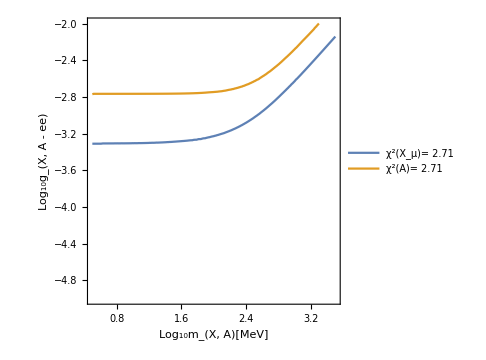

```mathematica
p2=ContourPlot[{(NP[10^y0/e,10^x0*10^-3]==2.71),(NPA[(10^y0*2*mW*√(1-cW^2))/(mme*e),10^x0*10^-3]==2.71)},{x0,5/10,35/10},{y0,-5,-2},BoundaryStyle->{Thick,Red}(*Khung đỏ xung quanh Plot*),FrameLabel->{"Log_10m_(X, A)[MeV]","Log_10g_(X, A - ee)"}(*tile cho trục*),LabelStyle->Directive[Orange,FontFamily->"Helvetica",12](*kiểu cho title*),FrameTicksStyle->{{Black,Black},{Black,Black}}(*kiểu cho trục*),FrameStyle->AbsoluteThickness[1](*tăng độ đậm của khung*),(*PlotLabel->Style[Framed[""](*title của plot*),16,White(*màu chữ cho title plot*),Background->Lighter[Gray, 0.5](*màu nền cho title plot*)],*)ImageSize->Medium(*kích cỡ plot*),PlotLegends->Placed[LineLegend[{"χ^2(X_μ)= 2.71","χ^2(A)= 2.71"}],{Left,Bottom}]]
```

```mathematica
Export["ChiXA_271.png",p2]
(*p3=DensityPlot[NP[Es/e,mX*10^-3],{mX,10^-3,10^2},{Es,10^-3.7*e,10^-2.7*e},PlotLegends->BarLegend[Automatic,LegendMarkerSize->180,LegendFunction->"Frame"(*Đóng khung chú thích*),LegendMargins->5,LegendLabel->"χ^2"(*Tên phần chú thích*),FrameStyle->Directive[Red,Thick](*kiểu cho khung chú thích*)],ScalingFunctions->{"Log10"(*plot range của trục x*),None(*plot range của trục y*)},PlotRange->All,BoundaryStyle->{Thick,Red}(*Khung đỏ xung quanh Plot*),FrameLabel->{"m_X[MeV]","g_Xff"}(*tile cho trục*),LabelStyle->Directive[Orange,FontFamily->"Helvetica",12](*kiểu cho title*),FrameTicksStyle->{{Black,Black},{Black,Black}}(*kiểu cho trục*),FrameStyle->AbsoluteThickness[1](*tăng độ đậm của khung*),(*PlotLabel->Style[Framed[""](*title của plot*),16,White(*màu chữ cho title plot*),Background->Lighter[Gray, 0.5](*màu nền cho title plot*)],*)ImageSize->Medium(*kích cỡ plot*),ColorFunction->"TemperatureMap",ScalingFunctions->{"Log10",None}]*)
```

ChiXA_271.png

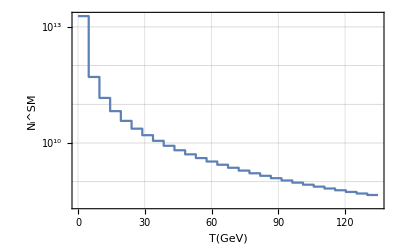

```mathematica
DataSM = Table[-5*L*GevToBarn*mme/ppeCM^2*-sigma0EW[1-mme/ppeCM^2*T]/.{t->t[1-mme/ppeCM^2*T],s->s[1-mme/ppeCM^2*T],u->u[1-mme/ppeCM^2*T]},{T,1,139,5}];
distrpic=ListStepPlot[DataSM,Frame->True,DataRange->{0,130},GridLines->Automatic,ScalingFunctions->"Log10",FrameLabel->{"T(GeV)","N_i^SM"}]
```

```mathematica
Export["distribution_SM_T_setup2.png",distrpic]
```

distribution_SM_T_setup2.png

```mathematica
DataVector= Table[10^5*(5*L*GevToBarn*mme/ppeCM^2*(+sigma0EW[1-mme/ppeCM^2*T]-sigma0EWG[1-mme/ppeCM^2*T,10^-3/e,100*10^-3]))/(5*L*GevToBarn*mme/ppeCM^2*(-sigma0EW[1-mme/ppeCM^2*T]))/.{t->t[1-mme/ppeCM^2*T],s->s[1-mme/ppeCM^2*T],u->u[1-mme/ppeCM^2*T]},{T,1,139,5}];
DataScalar= Table[10^5*(5*L*GevToBarn*mme/ppeCM^2*(+sigma0EW[1-mme/ppeCM^2*T]-sigma0E[1-mme/ppeCM^2*T,(2.4*10^-2*2*mW*√(1-cW^2))/(mme*e),100*10^-3]))/(5*L*GevToBarn*mme/ppeCM^2*(-sigma0EW[1-mme/ppeCM^2*T]))/.{t->t[1-mme/ppeCM^2*T],s->s[1-mme/ppeCM^2*T],u->u[1-mme/ppeCM^2*T]},{T,1,139,5}];(*currently Subscript[y, ee] Subscript[#y, μμ],but we need Subscript[y, ee]= Subscript[y, μμ] *)
```

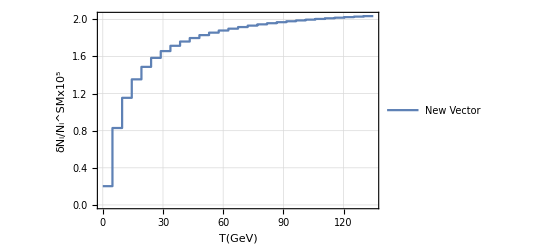

```mathematica
distrpicX=ListStepPlot[{DataVector},Frame->True,DataRange->{0,130},GridLines->Automatic,FrameLabel->{"T(GeV)","δN_i/N_i^SMx10^5"},PlotLegends->Placed[LineLegend[{"New Vector","New Scalart"}],{Right,Bottom}]]
```